# Performance Measurement - Profiling

#### Steps to performance measurement

Note: To time a short event, it is necessary to repeat it several times and divide the total time for the event by the number of repetitions.
1. Create two matrices of nxn size.
2. Add them up and measure the time (do this 50 times)
3. Store the measured time in a list (after dividing it by 50)
4. Repeat Step 1 to 3 for n=1 to 300.
5. Plot n versus time taken.

#### Get the timing for adding two matrices

```mathematica
timing=Table[First[Do[Plus[Array[Plus,{n,n}],Array[Plus,{n,n}]],{i,50}]//Timing]/50,{n,1,300}];
```

#### Plot the timing obtained

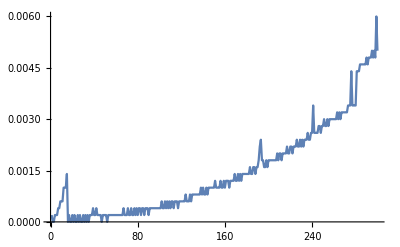

```mathematica
ListLinePlot[timing]
```

#### Compare with the shape of the curve of n^2

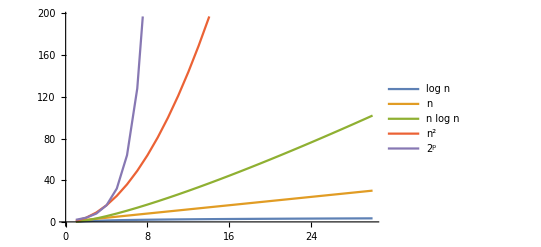

```mathematica
ListLinePlot[{Table[Log[p],{p,1,30}],Table[p,{p,1,30}],Table[p Log[p],{p,1,30}],Table[p^2,{p,1,20}],Table[2^p,{p,1,10}]},PlotLegends->{"log n","n","n log n","n^2","2^p"}]
```

Which of the plots best match the timings we obtained using profiling?

#### Search

```mathematica
timing=Table[First[MemberQ[RandomInteger[n,n],n+1]//Timing],{n,5000,50000}]
```

RandomInteger::unifr: The endpoints specified by 5001/2 for the endpoints of the discrete uniform distribution range are not integers.

General::stop: Further output of RandomInteger::unifr will be suppressed during this calculation.

$Aborted

```mathematica
First[MemberQ[RandomInteger[5000,500000],5001]//Timing]
```

0.32